{{-4,75},{-3,0},{-2,-9},{-1,0},{0,27},{1,0},{2,375}}

-4. | 75.
-3. | 0.
-2. | -9.
-1. | 0.
0. | 27.
1. | 0.
2. | 375.

-4.0 |  75.0
 -3.0 |   0.0
 -2.0 |  -9.0
 -1.0 |   0.0
  0.0 |  27.0
  1.0 |   0.0
  2.0 |  375.0

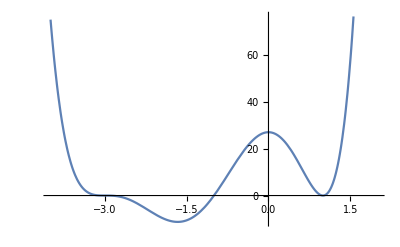

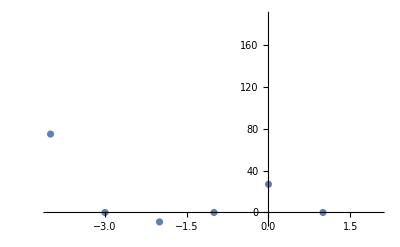

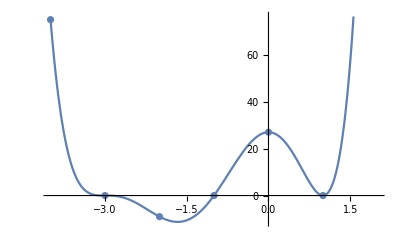

```mathematica
a=-4; b=2; n=7;
h=(b-a)/(n-1);

f[x] := x^6 + 8x^5 +17x^4 -8x^3 -45x^2 +27

tab1 = Table[{x = a +i*h, f[x]}, {i,0, n-1}]
tab2 = TableForm[N[tab1]]
tab3 = PaddedForm[tab2, {3,1}]

gr1 := Plot[f[x],{x,a,b}]; gr1
gr2 := ListPlot[tab1];gr2

Show[{gr1,gr2}]
```